## Introduction

Pics for paper here

## Static states

```mathematica
axisSize=30;
tickSize=17;
insetSize=20;
```

### Static sync

<k> = 1.25

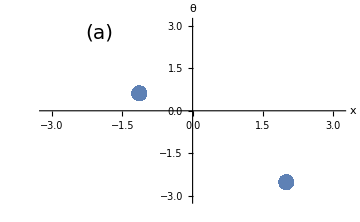
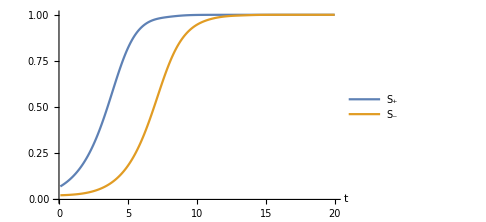
-Graphics- | -Graphics-

```mathematica
{dt,n,T}={0.1,500,20};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2}={0.3,-0.5,2};
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
Print["<k> = "<>ToString[Mean[ks]//N]]
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
z0=znew;t++;
{Wp,Wm}=findWs[znew];{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];
p1=ListPlot[{Mod[znew[[1,All]],2π]-π,Mod[znew[[2,All]],2π]-π}ᵀ,Epilog->{Text[Style["(a)",insetSize],{-2,2.75}]},PlotStyle->{PointSize[0.03]},LabelStyle->tickSize,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",axisSize],Style["θ",axisSize]}];
p2=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{Style["t",20,Italic]},PlotLegends->{"S_+","S_-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

### Static phase wave

<k> = -0.43

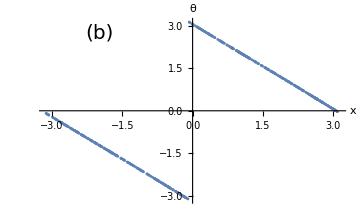
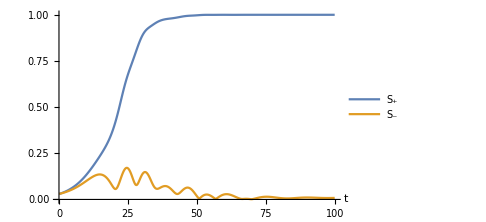
-Graphics- | -Graphics-

```mathematica
{dt,n,T}={0.1,500,100};
{p,k1,k2}={0.9,-0.5,0.2};
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
Print["<k> = "<>ToString[Mean[ks]//N]]
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
z0=znew;t++;
{Wp,Wm}=findWs[znew];{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];
p3=ListPlot[{Mod[znew[[1,All]],2π]-π,Mod[znew[[2,All]],2π]-π}ᵀ,LabelStyle->tickSize,Epilog->{Text[Style["(b)",insetSize],{-2,2.75}]},PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",axisSize],Style["θ",axisSize]}];
p4=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{Style["t",20,Italic]},PlotLegends->{"S_+","S_-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p3,p4}}]
```

### Buckled phase wave

<k> = -0.25

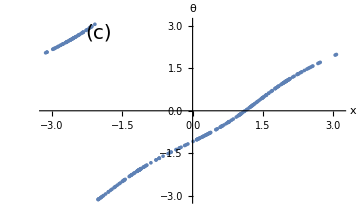
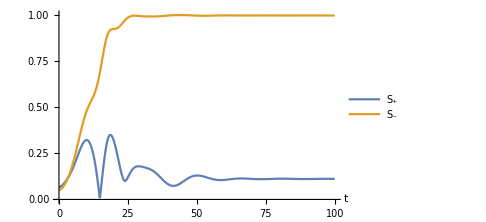
-Graphics- | -Graphics-

```mathematica
{dt,n,T}={0.1,300,100};
{p,k1,k2}={0.5,1,-1.5};
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
Print["<k> = "<>ToString[Mean[ks]//N]]
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
z0=znew;t++;{Wp,Wm}=findWs[znew];{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];
p5=ListPlot[{Mod[znew[[1,All]],2π]-π,Mod[znew[[2,All]],2π]-π}ᵀ,PlotRange->{{-π,π},{-π,π}},Epilog->{Text[Style["(c)",insetSize],{-2,2.75}]},LabelStyle->tickSize,ImageSize->Medium,AxesLabel->{Style["x",axisSize],Style["θ",axisSize]}];
p6=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{Style["t",20,Italic]},PlotLegends->{"S_+","S_-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p5,p6}}]
```

### Put together

```mathematica
pStatic=Grid[{{p1,p3,p5}}];
pStatic=Grid[{{p1,SpanFromLeft,p3},{SpanFromLeft,p5,SpanFromLeft}}]
Export["figures/static-states.png",pStatic];
```

-Graphics- |  | -Graphics-
 | -Graphics- |

## Bifurcation diagrams

### Bif diagram (p,Kn)

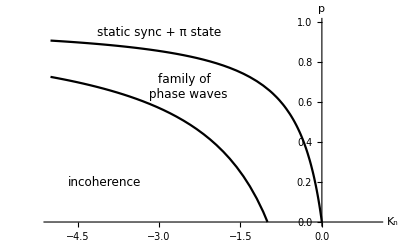

```mathematica
Clear[k1,k2,J]
p1=Plot[Evaluate[{(J+k2)/(-k1+k2),-k2/(k1-k2)}/.{k1->0.5,J->1}],{k2,-5,1},
PlotStyle->Black,PlotRange->{0,1},AxesLabel->{Style["K_n",Italic,17],Style["p",Italic,18]},
Epilog->{
Text[Style["static sync + π state",12],{-3,0.95}],
Text[Style["incoherence",12],{-4,0.2}],
Text[Style["family of \n phase waves",12],{-2.5,0.675}]
}
]

SetDirectory[NotebookDirectory[]];
Export["figures/bif-diagram.png",p1];
```

### Bif diagram

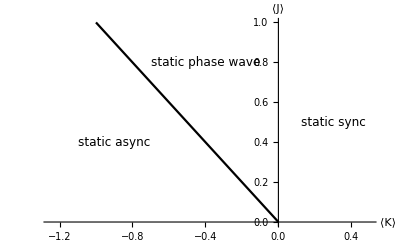

```mathematica
Clear[k1,k2,J]
p1=Plot[-k,{k,-1.25,0.5},
PlotStyle->Black,PlotRange->{0,1},AxesLabel->{Style["⟨K⟩",Italic,17],Style["⟨J⟩",Italic,18]},
Epilog->{
Text[Style["static async",12],{-0.9,0.4}],
Text[Style["static sync",12],{0.3,0.5}],
Text[Style["static phase wave",12],{-0.4,0.8}]
}
]
SetDirectory[NotebookDirectory[]];
Export["figures/bif-diagram-J-K.png",p1];
```

## Order parameters

#### Load data

Data from Hyunsuk

```mathematica
SetDirectory[NotebookDirectory[]];
fname="data/data/1101_1Dswarm_Kj_Q2.0_J1.0_N1600_samp20ave.dat";
data=Import[fname];
```

#### Plot

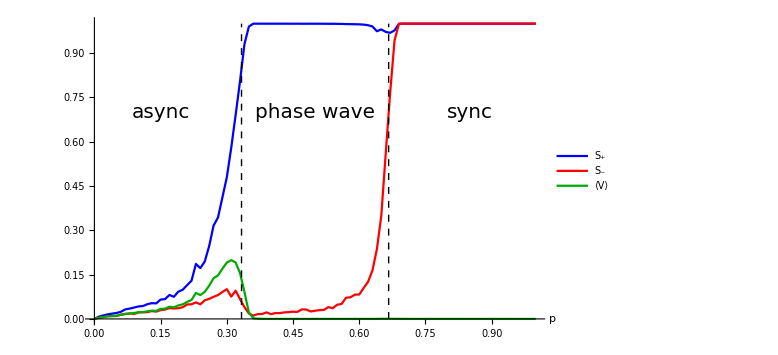

figures/order-pars.png

```mathematica
(*Presets*)
axisSize=35;
tickSize=20;
insetSize=20;
legendSize=25;

{k1,k2}={2,-1};
{pc,ps}={-k2/(k1-k2),(-1+k2)/(-k1+k2)};
p=data[[All,1]];
{Splus,Sminus,meanV}={data[[All,4]],data[[All,6]],data[[All,8]]};
p1=ListPlot[{{p,Splus}ᵀ,{p,Sminus}ᵀ,{p,meanV}ᵀ},Joined->True,
AxesLabel->{Style["p",Italic,axisSize]},TicksStyle->tickSize,ImageSize->Large,PlotStyle->{Blue,Red,Darker[Green]},
PlotLegends->{Style["S_+",Italic,legendSize],Style["S_-",Italic,legendSize],Style["⟨V⟩",Italic,legendSize]},
Epilog->{
Dashed,Line[{{pc,0},{pc,1}}],Line[{{ps,0},{ps,1}}],
Text[Style["sync",insetSize],{0.85,0.7}],Text[Style["phase wave",insetSize],{0.5,0.7}],
Text[Style["async",insetSize],{0.15,0.7}]
}
]

(*Save*)
SetDirectory[NotebookDirectory[]];
Export["figures/order-pars.png",p1]
```

## Buckle size(n)

### Methods

```mathematica
findBuckleWidth[znew_]:=Block[{x,θ,ξ,η,L,Wp,Wm},
{x,θ}=znew;
{ξ,η}={x+θ,x-θ}//mod;
{Wp,Wm}=findWs[znew];
If[Abs[Wp]<Abs[Wm],{ξ,η}={η,ξ}];
L=Max[ξ]-Min[ξ];
Return[L]
];
```

### L(u)

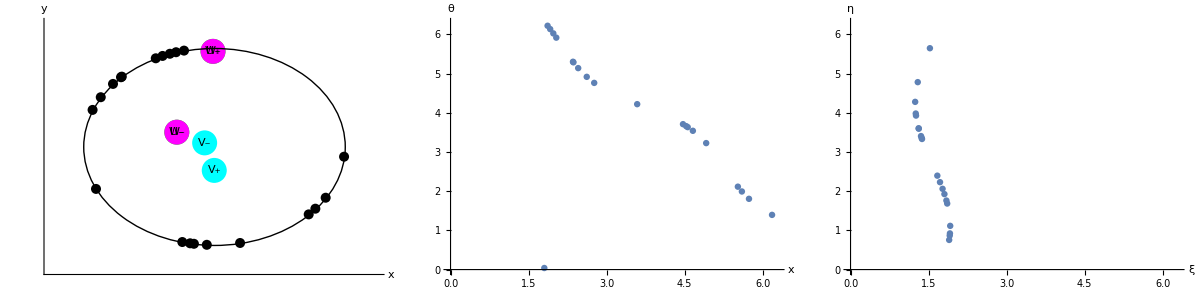

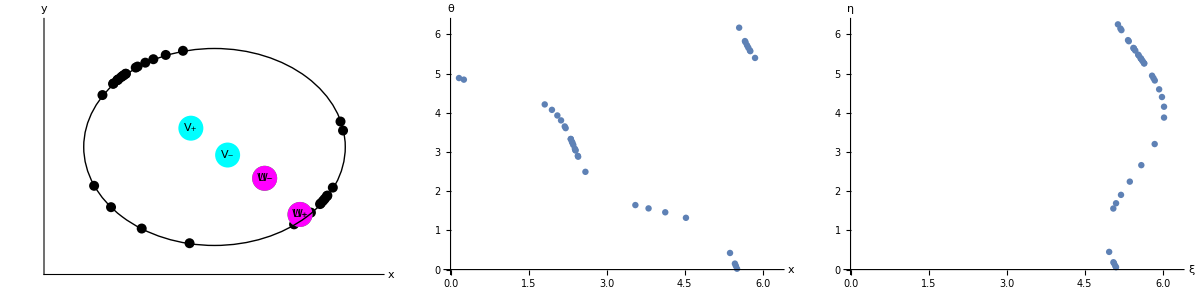

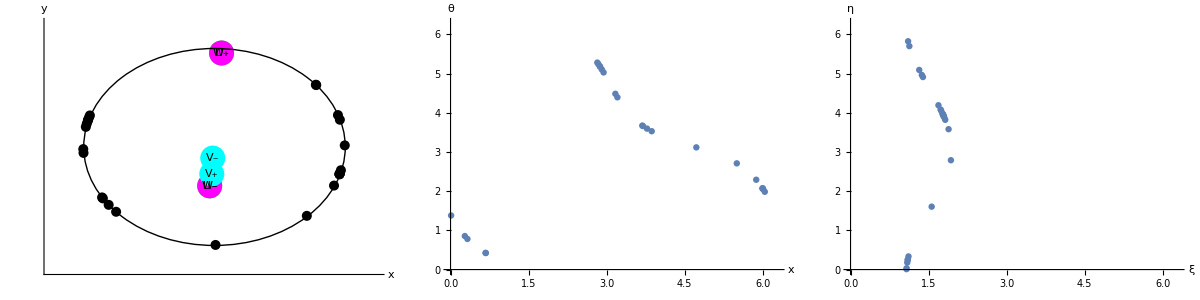

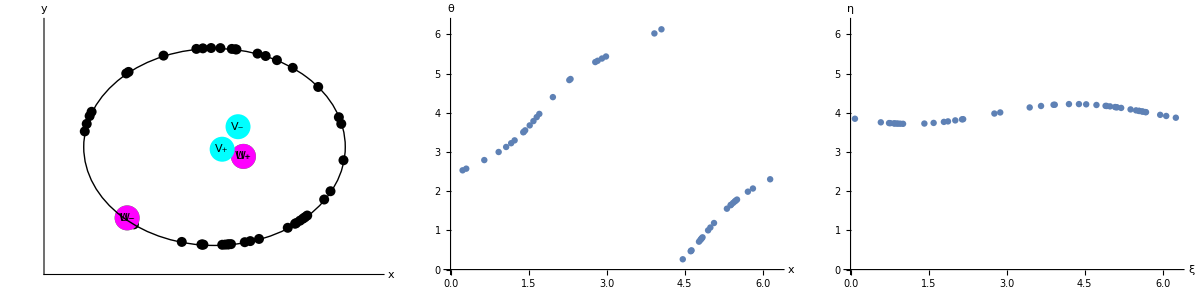

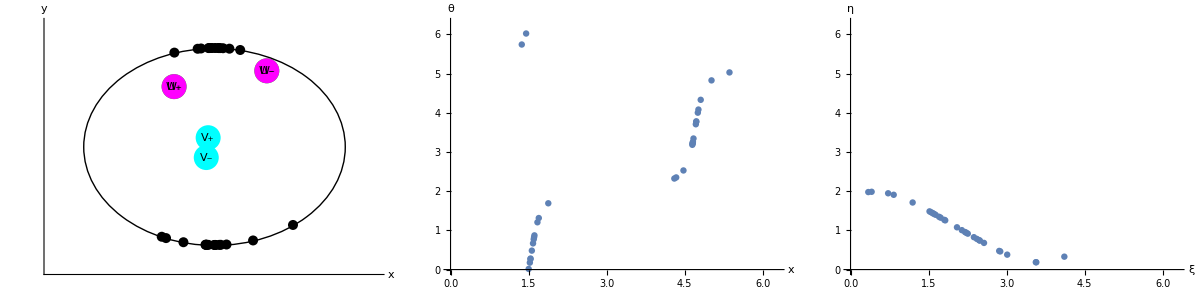

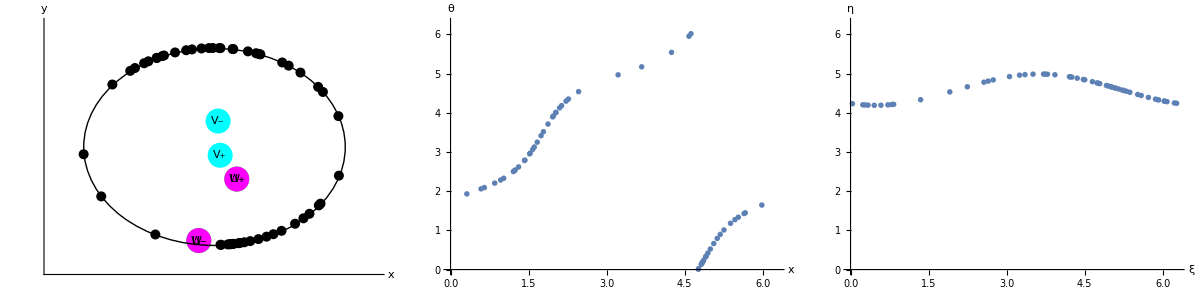

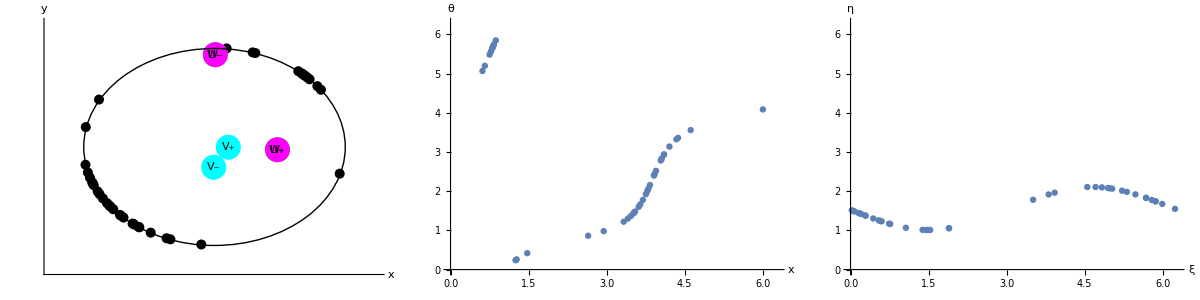

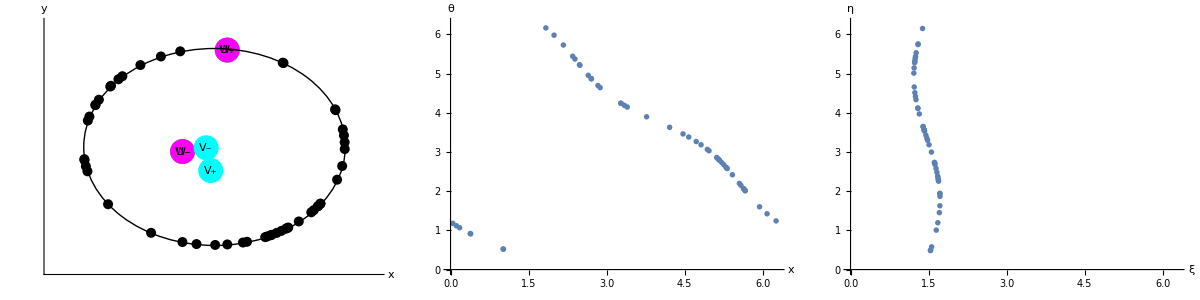

```mathematica
dataLu=ParallelTable[
SeedRandom[0];
{dt,T}={0.25,1000};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2}={0.5,1,-1.5};
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,Vps,Vms,ts}={{},{},{},{},{},{},{}};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
z0=znew;t++;
{ups,ums,Vp,Vm}=findVs[znew,js,ks];
If[Abs[ups]<Abs[ums],{ups,ums}={ums,ups}]
];
Print[plotResults[znew,js,ks]];
{n,Abs[ums]/Abs[ups],findBuckleWidth[znew]},
{n,20,100,5}
];

p1=ListPlot[dataLu[[All,{2,3}]],AxesLabel->{Style["u",17,Italic],Style["L",17,Italic]}];
p2=Plot[2 ArcSin[u],{u,0,2}];
Show[p1,p2]
```

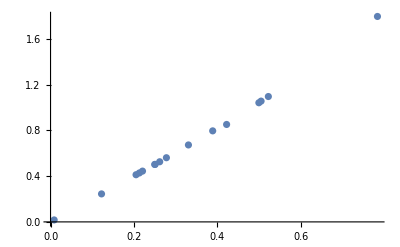

```mathematica
ListPlot[Delete[dataLu,4][[1;;-1,{2,3}]]]
```

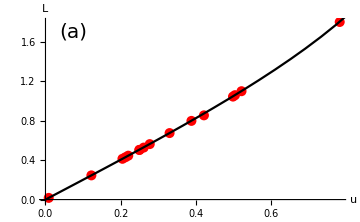

```mathematica
p1=ListPlot[Delete[dataLu,4][[1;;-1,{2,3}]],AxesLabel->{Style["u",25,Italic],Style["L",25,Italic]},TicksStyle->Directive["Label", 12],PlotStyle->{PointSize[0.02],Red},ImageSize->Medium,Epilog->{Text[Style["(a)",insetSize],{0.075,1.7}]}];
p2=Plot[2 ArcSin[u],{u,0,2},PlotStyle->Black];
pLu=Show[p1,p2]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figures/buckle-phase-wave-L-u.png",pLu];
```

### L(n)

#### Run sim

{100,0.213152,0.429765}

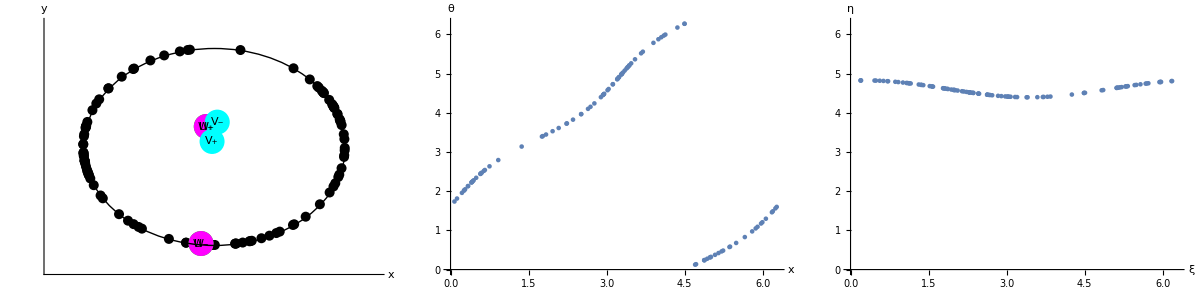

{500,0.158697,0.319153}

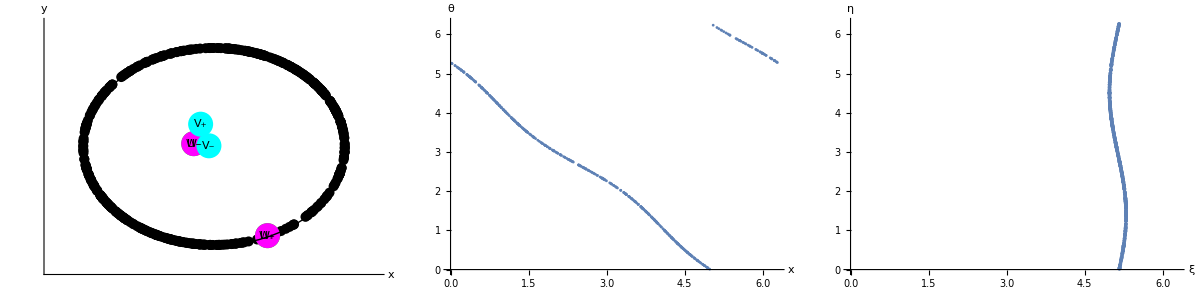

{1000,0.0131926,0.0279004}

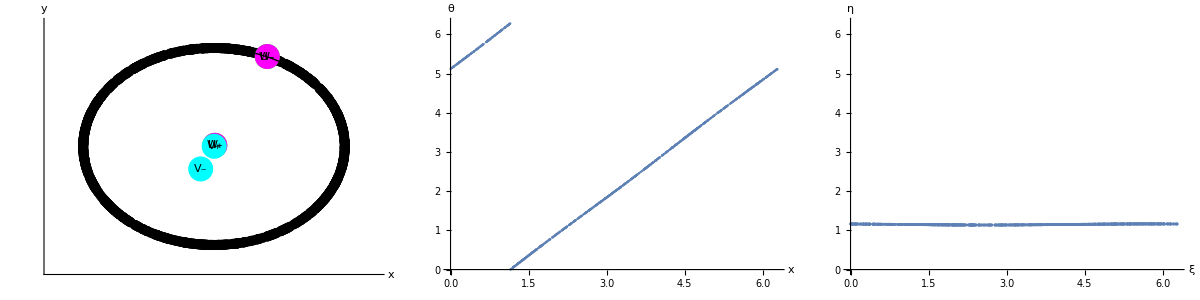

{2000,0.0634819,0.126157}

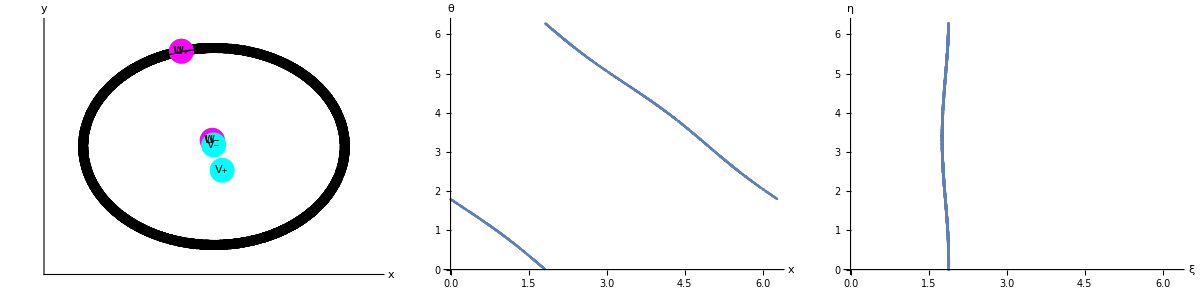

{5000,0.0503008,0.102654}

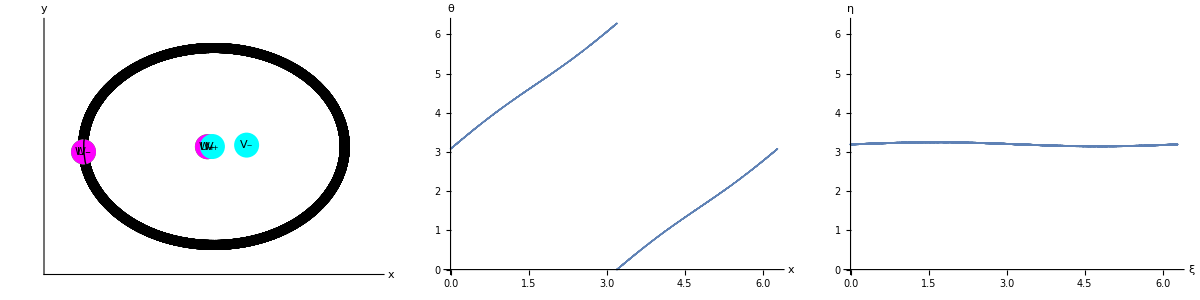

{8000,0.0274257,0.0541101}

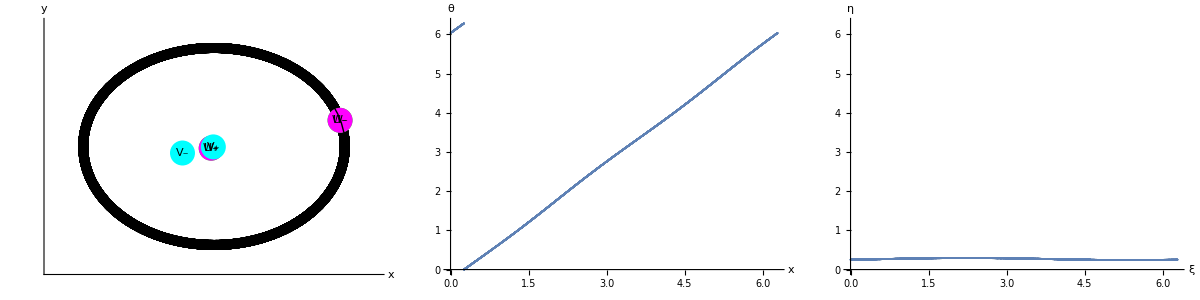

{6000,0.0213282,0.0423228}

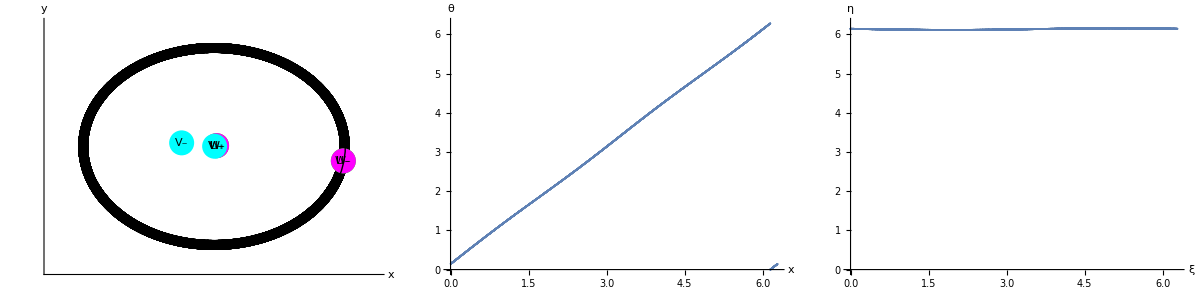

{10000,0.0264522,0.0577296}

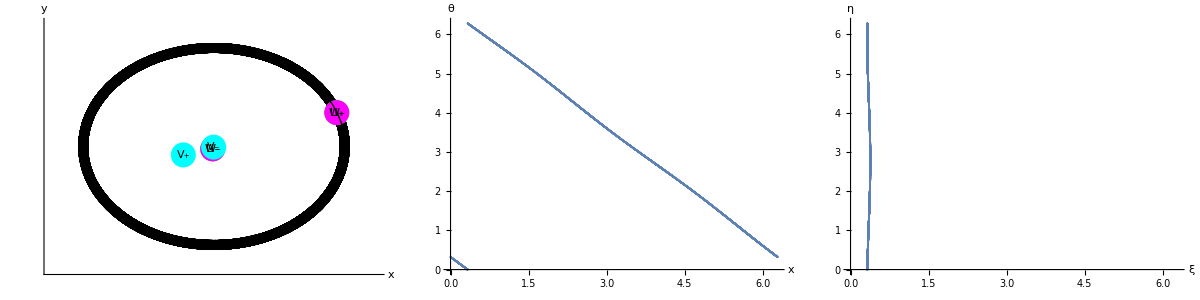

{20000,0.00348231,0.0113368}

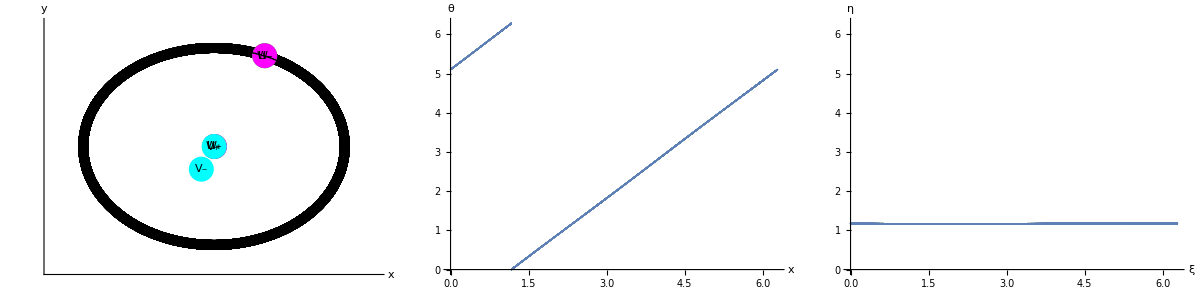

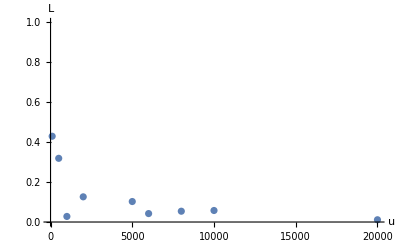

```mathematica
dataLn=ParallelTable[
SeedRandom[0];
{dt,T}={0.5,75};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2}={0.5,1,-1.5};
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,Vps,Vms,ts}={{},{},{},{},{},{},{}};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
z0=znew;t++;
{ups,ums,Vp,Vm}=findVs[znew,js,ks];
If[Abs[ups]<Abs[ums],{ups,ums}={ums,ups}]
];
Print[{n,Abs[ums]/Abs[ups],findBuckleWidth[znew]}];
Print[plotResults[znew,js,ks]];
{n,Abs[ums]/Abs[ups],findBuckleWidth[znew]},
{n,{100,500,1000,2000,5000,6000,8000,10000,20000}}
];
pLn=ListPlot[dataLn[[All,{1,3}]],AxesLabel->{Style["N",17,Italic],Style["L",17,Italic]},PlotRange->{0,1},TicksStyle->Directive["Label", 12]]
```

#### Save data

```mathematica
d={{100,0.42976506202755704},{500,0.31915325985738274},{1000,0.027900449125990434},{2000,0.12615656115273932},{5000,0.10265443989873724},{6000,0.04232283992188268},{8000,0.05411007895734965},{10000,0.05772959306046399},{20000,0.011336762638761488}};
```

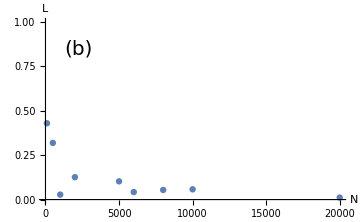

```mathematica
pLn=ListPlot[d,AxesLabel->{Style["N",25,Italic],Style["L",25,Italic]},PlotRange->{0,1},TicksStyle->Directive["Label", 12],ImageSize->Medium,Epilog->{Text[Style["(b)",insetSize],{2250,0.85}]}]
```

### Plot together

```mathematica
SetDirectory[NotebookDirectory[]];
pLu=Import["figures/buckle-phase-wave-L-u.png"];
```

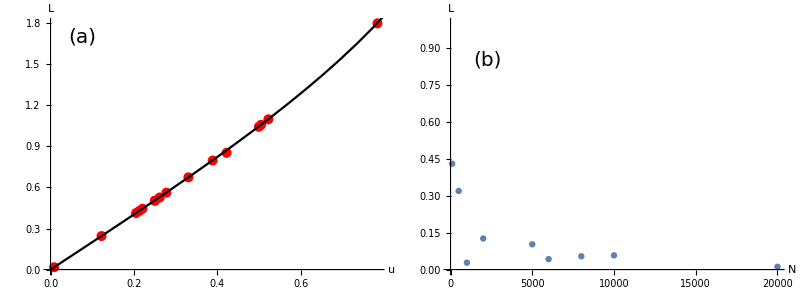

figures/buckle-phase-wave-finite-N.png

```mathematica
pTogether=Grid[{{pLu,pLn}}]
SetDirectory[NotebookDirectory[]];
Export["figures/buckle-phase-wave-finite-N.png",pTogether]
```

## Noisy phase waves

### Noisy phase wave

```mathematica
{dt,n,T}={0.5,500,1000};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2}={0.3,1,-2};
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
{z0,znew}={Table[RandomReal[{0,0.01}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
z0=znew;t++;
{Wp,Wm}=findWs[znew];{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];
```

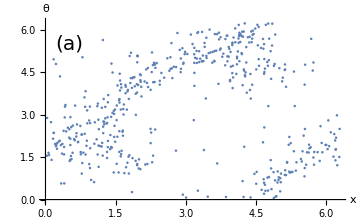
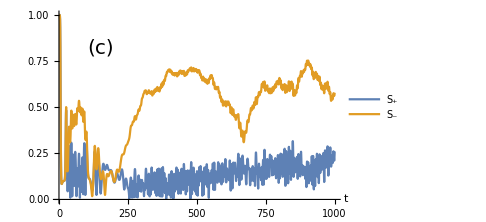
-Graphics- | -Graphics-

```mathematica
p1=ListPlot[{Mod[znew[[1,All]],2π],Mod[znew[[2,All]],2π]}ᵀ,PlotRange->{{0,2π},{0,2π}},ImageSize->Medium,AxesLabel->{Style["x",Italic,axisSize],Style["θ",Italic,axisSize]},Epilog->{Text[Style["(a)",insetSize],{0.5,5.5}]},LabelStyle->tickSize,PlotStyle->{PointSize[0.005]}];
p2=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{Style["t",axisSize,Italic]},PlotLegends->{Style["S_+",20],Style["S_-",20]},Joined->True,ImageSize->Medium,PlotRange->{0,1},Epilog->{Text[Style["(c)",insetSize],{150,0.82}]},LabelStyle->tickSize];
Grid[{{p1,p2}}]
```

### Active async

```mathematica
{dt,n,T}={0.5,500,2000};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2}={0.45,5,-7};
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
{z0,znew}={Table[RandomReal[{0,0.01}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
z0=znew;t++;
{Wp,Wm}=findWs[znew];{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];
```

$Aborted

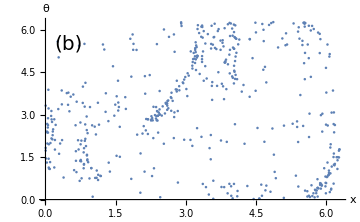
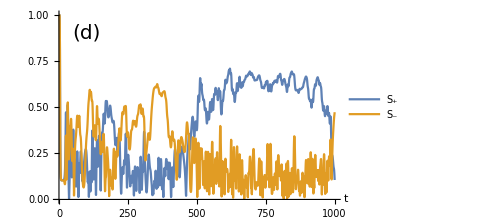
-Graphics- | -Graphics-

```mathematica
p3=ListPlot[{Mod[znew[[1,All]],2π],Mod[znew[[2,All]],2π]}ᵀ,PlotRange->{{0,2π},{0,2π}},ImageSize->Medium,AxesLabel->{Style["x",Italic,axisSize],Style["θ",Italic,axisSize]},Epilog->{Text[Style["(b)",insetSize],{0.5,5.5}]},LabelStyle->tickSize,PlotStyle->{PointSize[0.005]}];
p4=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{Style["t",axisSize,Italic]},PlotLegends->{Style["S_+",20],Style["S_-",20]},Joined->True,ImageSize->Medium,PlotRange->{0,1},Epilog->{Text[Style["(d)",insetSize],{100,0.9}]},LabelStyle->tickSize];
Grid[{{p3,p4}}]
```

### Save fig

```mathematica
pboth=Grid[{{p1,p3},{p2,p4}}]
SetDirectory[NotebookDirectory[]];
Export["figures/phase-wave-async.png",pboth]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

figures/phase-wave-async.png

## Functions

```mathematica
rhs=Compile[{{z,_Real,2},{n,_Integer},{J,_Real,1},{k,_Real,1}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,inverseDist,xtemp,ytemp,thetatemp,rep,A,B,C,n1,vel=ConstantArray[0.0,{2,n}]},
{A,B,C,n1}={1,1,10,1};
For[i=1,i≤n,i++,
For[j=1,j≤n,j++,
If[j≠i,
xji=z[[1,j]]-z[[1,i]];
thetaji=z[[2,j]]-z[[2,i]];
xtemp=J[[j]]*Sin[xji] Cos[thetaji];
thetatemp=k[[j]]*Sin[thetaji] Cos[xji];
vel[[1,i]]+=xtemp;
vel[[2,i]]+=thetatemp;
]
];
];
vel/N[n]
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

findWs[z_]:=Block[{Wp,Wm,i,numOsc},
{Wp,Wm}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Wp+=Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Wm+=Exp[ⅈ (z[[1,i]]-z[[2,i]])];
];
Return[{Wp/numOsc,Wm/numOsc}]
];

findVs[z_,j_,k_]:=Block[{Upos,Um,Vp,Vm,i,numOsc},
{Upos,Um,Vp,Vm}={0,0,0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Upos+=j[[i]]*Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Um+=j[[i]]*Exp[ⅈ (z[[1,i]]-z[[2,i]])];
Vp+=k[[i]]*Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Vm+=k[[i]]*Exp[ⅈ (z[[1,i]]-z[[2,i]])];
];
Return[{Upos/numOsc,Um/numOsc,Vp/numOsc,Vm/numOsc}]
];

findRs[z_]:=Block[{Z,Y,i,numOsc},
{Z,Y}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Y+=Exp[ⅈ (z[[1,i]])];
Z+=Exp[ⅈ (z[[2,i]])];
];
Return[{Y/numOsc,Z/numOsc}]
]

plotResults[z_,js_,ks_]:=Block[{colors,Wp,Wm,Vp,Vm,Rx,Rtheta,p1,p2,p3},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[2,All]],2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];
{Rx,Rtheta}=findRs[z];
{Upos,Um,Vp,Vm}=findVs[z,js,ks];
p1=Graphics[{

(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],
Green,Point[{Wp//Re,Wp//Im}],Black,Text["W_+",{Wp//Re,Wp//Im}],
Green,Point[{Wm//Re,Wm//Im}],Black,Text["W_-",{Wm//Re,Wm//Im}],
Magenta,Point[{Upos//Re,Upos//Im}],Black,Text["U_+",{Upos//Re,Upos//Im}],
Magenta,Point[{Um//Re,Um//Im}],Black,Text["U_-",{Um//Re,Um//Im}],
Cyan,Point[{Vp//Re,Vp//Im}],Black,Text["V_+",{Vp//Re,Vp//Im}],
Cyan,Point[{Vm//Re,Vm//Im}],Black,Text["V_-",{Vm//Re,Vm//Im}],

(*Domain*)
Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];
p2=ListPlot[{Mod[z[[1,All]],2π],Mod[z[[2,All]],2π]}ᵀ,PlotRange->{{0,2π},{0,2π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];
p3=ListPlot[{Mod[z[[1,All]]+z[[2,All]],2π],Mod[z[[1,All]]-z[[2,All]],2π]}ᵀ,PlotRange->{{0π,2π},{0π,2π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];
Return[Grid[{{p1,p2,p3}}]
]
];


eulerStep1D[z_,F_,dt_,J_,k_]:=Block[{znew,n,i,j,vel},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
vel=F[z,n,J,k];
znew=z+dt*vel;
Return[znew]
];

rk4[z_,F_,dt_,J_,k_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,k];
k2=F[z+dt/2 k1,n,J,k];
k3=F[z+dt/2 k2,n,J,k];
k4=F[z+dt k3,n,J,k];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

mod[θ_]:=Return[Mod[θ,2π]-π];

findMeanV[znew_,z_,dt_]:=Block[{v},
v=(znew-z)/dt;
v=(v[[1,All]]^2+v[[2,All]]^2)^(1/2);
Return[Mean[v]]
];

findBuckleWidth[znew_]:=Block[{x,θ,ξ,η,L,Wp,Wm},
{x,θ}=znew;
{ξ,η}={x+θ,x-θ}//mod;
{Wp,Wm}=findWs[znew];
If[Abs[Wp]<Abs[Wm],{ξ,η}={η,ξ}];
L=Max[ξ]-Min[ξ];
Return[L]
];

plotResultsCustom[z_,p_,K1_,K2_,label_]:=Block[{colors,Wp,Wm,p1,p2,p3},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[2,All]],2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];
{Rx,Rtheta}=findRs[z];
{Upos,Um,Vp,Vm}=findVs[z,js,ks];
p1=Graphics[{

(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],
Green,Point[{Wp//Re,Wp//Im}],Black,Text["W_+",{Wp//Re,Wp//Im}],
Green,Point[{Wm//Re,Wm//Im}],Black,Text["W_-",{Wm//Re,Wm//Im}],
Magenta,Point[{Upos//Re,Upos//Im}],Black,Text["U_+",{Upos//Re,Upos//Im}],
Magenta,Point[{Um//Re,Um//Im}],Black,Text["U_-",{Um//Re,Um//Im}],
Cyan,Point[{Vp//Re,Vp//Im}],Black,Text["V_+",{Vp//Re,Vp//Im}],
Cyan,Point[{Vm//Re,Vm//Im}],Black,Text["V_-",{Vm//Re,Vm//Im}],

(*Domain*)
Black,Circle[{0,0},1]

},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium,PlotLabel->Style[label,15,Black]];
p2=ListPlot[{z[[1,All]]//mod,z[[2,All]]//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];
p3=ListPlot[{z[[1,All]]+z[[2,All]],z[[1,All]]-z[[2,All]]}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];
Return[Grid[{{p1,p2,p3}}]
]
];
```